## Plot tables with ArrayPlot

```mathematica
Table[Subscript[x, i] Subscript[y, j],{i,1,5},{j,1,10}]//MatrixForm
```

(x_1 y_1 | x_1 y_2 | x_1 y_3 | x_1 y_4 | x_1 y_5 | x_1 y_6 | x_1 y_7 | x_1 y_8 | x_1 y_9 | x_1 y_10
x_2 y_1 | x_2 y_2 | x_2 y_3 | x_2 y_4 | x_2 y_5 | x_2 y_6 | x_2 y_7 | x_2 y_8 | x_2 y_9 | x_2 y_10
x_3 y_1 | x_3 y_2 | x_3 y_3 | x_3 y_4 | x_3 y_5 | x_3 y_6 | x_3 y_7 | x_3 y_8 | x_3 y_9 | x_3 y_10
x_4 y_1 | x_4 y_2 | x_4 y_3 | x_4 y_4 | x_4 y_5 | x_4 y_6 | x_4 y_7 | x_4 y_8 | x_4 y_9 | x_4 y_10
x_5 y_1 | x_5 y_2 | x_5 y_3 | x_5 y_4 | x_5 y_5 | x_5 y_6 | x_5 y_7 | x_5 y_8 | x_5 y_9 | x_5 y_10)

```mathematica
Reverse[Table[Subscript[x, i] Subscript[y, j],{i,1,5},{j,1,10}]ᵀ]//MatrixForm
```

(x_1 y_10 | x_2 y_10 | x_3 y_10 | x_4 y_10 | x_5 y_10
x_1 y_9 | x_2 y_9 | x_3 y_9 | x_4 y_9 | x_5 y_9
x_1 y_8 | x_2 y_8 | x_3 y_8 | x_4 y_8 | x_5 y_8
x_1 y_7 | x_2 y_7 | x_3 y_7 | x_4 y_7 | x_5 y_7
x_1 y_6 | x_2 y_6 | x_3 y_6 | x_4 y_6 | x_5 y_6
x_1 y_5 | x_2 y_5 | x_3 y_5 | x_4 y_5 | x_5 y_5
x_1 y_4 | x_2 y_4 | x_3 y_4 | x_4 y_4 | x_5 y_4
x_1 y_3 | x_2 y_3 | x_3 y_3 | x_4 y_3 | x_5 y_3
x_1 y_2 | x_2 y_2 | x_3 y_2 | x_4 y_2 | x_5 y_2
x_1 y_1 | x_2 y_1 | x_3 y_1 | x_4 y_1 | x_5 y_1)

```mathematica
testData=Table[If[i>j,1,0],{i,1,10},{j,1,20}];
%//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

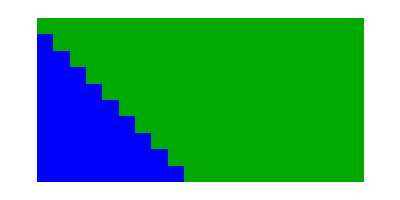

```mathematica
ArrayPlot[testData,ColorRules->{0->Darker[Green],1->Blue}]
```

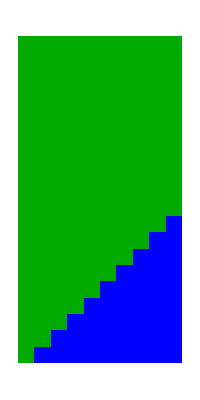

```mathematica
ArrayPlot[testDataᵀ,ColorRules->{0->Darker[Green],1->Blue},DataReversed->True]
```

## Example with CellularAutomaton

```mathematica
?ArrayPlot
```

ArrayPlot[array] generates a plot in which the values in an array are shown in a discrete array of squares.

```mathematica
CellularAutomaton[30,{{1,0,0,0,1,0,1,0},0},15]//ArrayPlot[#,Frame->False,Mesh->True,AspectRatio->1/GoldenRatio,MeshStyle->LightRed]&
```

-Graphics-